# InlämingUppgift

## Lucas Larsson collaboration with Dennis Hadzialic lulars@kth.se denhad@kth.se

## 1. Uppgift 1

### Show in ℝ^3 the solution set to the following equation Piecewise[{{z≥√(x^2+y^2) x^2+y^2+z^2≤1, }}]

```mathematica
cone=RegionPlot3D[z≥√(x^2+y^2),{x,-1,1},{y,-1,1},{z,-1,1},PlotTheme->"Detailed",AxesLabel->Automatic,PlotStyle->Red]
```

-Graphics3D-

```mathematica
sphere=RegionPlot3D[x^2+y^2+z^2≤1,{x,-2,2},{y,-2,2},{z,-2,2},PlotTheme->"Detailed",AxesLabel->Automatic,PlotStyle->Blue]
```

-Graphics3D-

```mathematica
RegionPlot3D[{z≥√(x^2+y^2),x^2+y^2+z^2≤1},{x,-2,2},{y,-2,2},{z,-2,2},PlotTheme->"Detailed",AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Show[cone,sphere]
```

-Graphics3D-

```mathematica
SolutionSet =Reduce[ {z≥√(x^2+y^2),x^2+y^2+ z^2≤1},{x,y,z}] ;
```

```mathematica
RegionPlot3D[{SolutionSet},{x,-1,1},{y,-1,1},{z,-1,1},PlotTheme->"Detailed",AxesLabel->Automatic]
```

-Graphics3D-

### Method

z≥√(x^2+y^2)
x^2+y^2+z^2≤1
this problem is solved using the function “Reduce” to calculate the solution set of the 2 equations. 
the first equation is a infinite cone, the second equation is a Sphere with the diameter of 1, the solution set is then plotted and showed above using the function “Show”.

## 2. Uppgift 2

### Calculate the Angel θ between the two vectors b and a a=2i-2j-2k b=3i-2j-k

```mathematica
Clear[a,b]
```

```mathematica
a = {2,-2,-2};
```

```mathematica
b= {3,-2,-1};
```

```mathematica
ArcCos[(a.b)/(Norm[a]*Norm[b])];
```

```mathematica
N[ArcCos[√(6/7)]]
```

0.387597

```mathematica
With[{d=N[ArcCos[√(6/7)]/°]},Defer[d °]]
```

22.2077 °

### Method

this problem solved using the equation"Cos(θ)=[(a . b)/(Norm[a]*Norm[b])]", θ  is the angel build by the vectors (a) and (b).
to get  the precises measurement of the angel θ  the function ArcCos is used, and then the value is approximated using the numerical solve function.

## 3. Uppgift 10

### Prove that the following matrix (A )has Orthogonal Columns. A= (-6 | -3 | 6 | 1 -1 | 2 | 1 | -6 3 | 6 | 3 | -2 6 | -3 | 6 | -1 2 | -1 | 2 | 3 -3 | 6 | 3 | 2 -2 | -1 | 2 | -3 1 | 2 | 1 | 6)

the columns of a matrix are orthogonal if the dot product of them is 0.

```mathematica
v1={-6,-1,  3,   6,   2,-3, -2, 1};
v2={-3,  2,   6, -3,-1, 6,  -1, 2};
v3={  6,   1,   3,   6,    2,  3,  2,  1};
v4={  1,-6, -2,-1,   3,   2,-3,6};
```

```mathematica
v1.v2
```

0

```mathematica
v1.v3
```

0

```mathematica
v1.v4
```

0

```mathematica
v2.v3
```

0

```mathematica
v2.v4
```

0

```mathematica
v3.v4
```

0

### Method

As mentioned above a Matrix columns are orthogonal if the dot product of the vectors is 0.
the matrix is later divided into 4 vectors and and multiplied to test if the columns are orthogonal.
the result of all the vectors dot product multiplication is 0 that means the columns are orthogonal. 
only 6 cases are tried since the dot product of two vectors is commutative i.e. (a.b = b.a).

## 4. Uppgift 4

### Calculate the Crossproduct of the folowing vectors according to the folowing u "×(v×w)". u=2i+3j-2k v=4i- j - k w=-4i-j+2k

```mathematica
u= {2,3,-2};
v={4,-1,-1};
w={-4,-1,2};
```

```mathematica
u×(v×w)
```

{-32,22,1}

### Method

this problem is solved as shown above, nothing to explain, worth to mention that it has to be in this exact order otherwise will get faulty answer since vectors (ab != ba).

## 5. Uppgift 5

### Solve the folowing equation system using graphs. Piecewise[{{x-2y=3 3x+5y=17, }}]

```mathematica
equation1=(x-3)/2;
```

```mathematica
equation2=(17-3x)/5;
```

```mathematica
Reduce[{x-2y==3,3x+5y==17},{x,y,z}]
```

x==49/11&&y==8/11

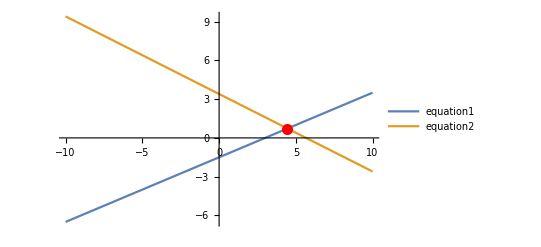

```mathematica
Plot[{equation1,equation2},{x,-10,10},Epilog->{Red, PointSize[0.02],Point[{49/11,8/11}]} ,PlotLegends->"Expressions"]
```

### Method

this equation set is solved using graphs for an approximate answer as stated in the task. 
the equations are rewritten as functions of X to be plotted. 
for an exact answer the function Reduce is used and then the point of intersection is marked using the point function.

## 6. Uppgift 9

### Find the Eigenvalues for the following matrix. (9 | -4 | -2 | -2 -56 | 32 | -28 | 44 -14 | -14 | 6 | -14 42 | -33 | 21 | -45)

```mathematica
Clear[matrixA]
```

```mathematica
matrixA={{9,-4,-2,-4},{-56,32,-28,44 },{-14,-14,6,-14},{42,-33,21,-45}};
```

```mathematica
matrixA//MatrixForm
```

(9 | -4 | -2 | -4
-56 | 32 | -28 | 44
-14 | -14 | 6 | -14
42 | -33 | 21 | -45)

```mathematica
Eigenvalues[matrixA]
```

{13,13,-12,-12}

### Method

the Matrix is declared as list of lists as required by Mathematica soft-wear for it to be computed, the function EigenValues is then used to compute the task solution.

## 7. Uppgift 7

### Calculate A-B+C,ABC, and CBA . A=(3 7 2 | 2 12 5 | 4 0 2),B=(5 6 10 | 8 4 1 | 7 9 0),C=(5 5 6 | 22 9 8 | 5 7 2).

```mathematica
Clear[A,B,c]
```

```mathematica
A={{3,2,4},{7,12,0},{2,5,2}};
```

```mathematica
B={{5,8,7},{6,4,9},{10,1,0}};
```

```mathematica
c={{5,22,5},{5,9,7},{6,8,2}};
```

```mathematica
result1=A-B+c;
```

```mathematica
result1//MatrixForm
```

(3 | 16 | 2
6 | 17 | -2
-2 | 12 | 4)

```mathematica
result2= A.B.c;
```

```mathematica
result2//MatrixForm
```

(749 | 2110 | 665
1997 | 4546 | 1577
844 | 2134 | 684)

```mathematica
result3=c.B.A;
```

```mathematica
result3//MatrixForm
```

(2018 | 3175 | 1294
1260 | 1874 | 828
1096 | 1750 | 620)

### Method

the function Clear is used t avoid declaring conflicts between other tasks/cells, the matrix is rewritten as a list of lists as in previous task, the specified tasks are then computed as shown in the result section above, matrices noncommutative feature is demonstrated above through computing ABC and CBA, the results are different as expected.

## 8. Uppgift 18

### State the DiagonalMatrix D and matrices P and P^-1 of A. A=(-6 | 4 | 0 | 9 -3 | 0 | 1 | 6 -1 | -2 | 1 | 0 -4 | 4 | 0 | 7)

The following formula “A = PDP^-1” is used to solve the above mentioned problem.

```mathematica
Clear[A,P]
```

```mathematica
A={{-6,4,0,9},{-3,0,1,6},{-1,-2,1,0},{-4,4,0,7}};
```

```mathematica
A//MatrixForm
```

(-6 | 4 | 0 | 9
-3 | 0 | 1 | 6
-1 | -2 | 1 | 0
-4 | 4 | 0 | 7)

```mathematica
Eigenvalues[A]
```

{5,-2,-2,1}

```mathematica
d={{5,0,0,0},{0,-2,0,0},{0,0,-2,0},{0,0,0,1}};
```

```mathematica
d//MatrixForm
({{5, 0, 0, 0}, {0, -2, 0, 0}, {0, 0, -2, 0}, {0, 0, 0, 1}});
```

(5 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 | 0
0 | 0 | 0 | 1)

```mathematica
Eigenvectors[A];
```

```mathematica
P =Transpose[Eigenvectors[A]];
P//MatrixForm
```

(2 | 6 | 1 | 2
1 | -3 | 1 | -1
-1 | 0 | 1 | -7
2 | 4 | 0 | 2)

```mathematica
PInverse=Inverse[P];
```

```mathematica
PInverse//MatrixForm
```

(-5/14 | 2/7 | 1/14 | 3/4
2/21 | -1/7 | 1/21 | 0
17/21 | 2/7 | -2/21 | -1
1/6 | 0 | -1/6 | -1/4)

```mathematica
P.d.PInverse//MatrixForm
```

(-6 | 4 | 0 | 9
-3 | 0 | 1 | 6
-1 | -2 | 1 | 0
-4 | 4 | 0 | 7)

### Method

the formal “A = PDP^-1” is used to compute the diagonal matrix D and then to test the results.
the functions used to solve this task are EigenValues, EigenVectors, Inverse and Transpose, the Diagonal matrix ”d” is constructed using the function  EigenValues, and then to test the results P is constructed using the EigenVectors function, inverse is used to get the inverted matrix and the Transpose to get the vectors as columns of a matrix not Raws as they were created. 
P,D and P^-1 are multiplied to check the answer and the matrix A is generated as a result, i.e its correct answer.

## 9. Uppgift 13

### Prove the the Matrix A is regular and calculate the equilibrium vectors. Ax=(0.4 | 0.2 | 0.7 0 | 0.6 | 0.1 0.6 | 0.2 | 0.2)

A Matrix “A “ is regular if it has a inverse matrix.
A Matrix “ A” has an inverse Matrix if the determinant !=0

```mathematica
Ax={{0.4,0.2,0.7},
    {0,0.6,0.1},
    {0.6,0.2,0.2}};
Ax//MatrixForm
```

(0.4 | 0.2 | 0.7
0 | 0.6 | 0.1
0.6 | 0.2 | 0.2)

```mathematica
Det[Ax]
```

-0.2

Equilibrium vectors are computed using  by the formal "(Ax-I)x=0"

```mathematica
IM=IdentityMatrix[3];
IM//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Ax-IM//MatrixForm
```

(-0.6 | 0.2 | 0.7
0 | -0.4 | 0.1
0.6 | 0.2 | -0.8)

```mathematica
RowReduce[Ax-IM]//MatrixForm
```

(1 | 0. | -1.25
0 | 1 | -0.25
0 | 0 | 0)

```mathematica
{{x->1.25 z,y->0.25 z}}/.Rule->Equal
```

{{x==1.25 z,y==0.25 z}}

```mathematica
x={1.25,.25,1};
```

```mathematica
X={5,1,4};
```

the vector X elements are then divided by the sum of the elements.
solution : Equilibrium vector  q = { 0.5,  0.1 , 0.4};

### Method and discussion

As mentioned above Matrix  is regular if it has a inverse matrix.
and Matrix has an inverse Matrix if the determinant !=0.
the determinant is computed to -0.2, and thereby the matrix is regular. 

the Equilibrium vector is calculated using the formal “(Ax-I)x=0”.
the expression (Ax-I) is Solved using the RowReduce function, the result is then rewritten with the X3 as 4 to avoid fractions, the elements of the solution are then divided by the sum of the elements to get the Equilibrium vector q.
the method used to solve this problem is inspired from the course literature page 260.

## 10. Uppgift 15

### Determin if the following polynoms form a base in the vectorrum ℙ_3. { 5-3t+4 t^2+2 t^3, 9+ t +8 t^2-6 t^3, 6-2t+5 t^2, t^2}

the polynomial coefficient form a matrix A.

```mathematica
A=({{5, -3, 4, 2}, {9, 1, 8, -6}, {6, -2, 5, 0}, {0, 0, 1, 0}});
```

```mathematica
RowReduce[A]//MatrixForm
```

(1 | 0 | 0 | -1/2
0 | 1 | 0 | -3/2
0 | 0 | 1 | 0
0 | 0 | 0 | 0)

as shown above the matrix is linearly dependent and that’s why it can not compose a base in ℙ_3

### Method

For polynomials to be able to form basis in  ℙ_3 the vectors represented by there coefficients has to be linearly independent.
after composing the matrix A, A is row reduced and as shown above the vectors that form matrix A are linearly dependent and that’s why it is not possible for the above stated polynomials to form a base in ℙ_3.

## 11. Uppgift 3

```mathematica
Clear[P]
```

```mathematica
Reduce[{x+2y+3z==1,2x+4y+7z==2,3x+7y+11z==8}]
```

z==0&&y==5&&x==-9

```mathematica
P=({{-9, 5, 0}});
```

```mathematica
pt=Point[P];
```

```mathematica
P//MatrixForm
```

(-9 | 5 | 0)

```mathematica
plotPoint=Graphics3D[{AbsolutePointSize[10],Green,pt}];
```

```mathematica
plan1=ContourPlot3D[x+2y+3z==1,{x,-10,10},{y,-10,10},{z,-10,10},ContourStyle->Red];
```

```mathematica
plan2=ContourPlot3D[2x+4y+7z==2,{x,-10,10},{y,-10,10},{z,-10,10},ContourStyle->Blue];
```

```mathematica
plan3=ContourPlot3D[3x+7y+11z==8,{x,-10,10},{y,-10,10},{z,-10,10},ContourStyle->Yellow];
```

```mathematica
Show[plan1,plan2,plan3,plotPoint]
```

-Graphics3D-

### Method

the set of equations are plotted using the function ContourPlot3D, the set of functions meet at the point of solution, to find the exact point the function reduce is used, a object of type point is then created using the solution set point (-9,5 ,0). all plots are shown simultaneously with the function Show for a clearer picture of the solution and the point of intersection.